# Newton’s Method in ℂ

Newton’s method 
	z_(n+1)=z_n-f(z_n)/f'(z_n)
produces a sequence of z_n∈ℂ for any z_0 that hopefully converges to a root of f(z)=0.

```mathematica
f[z_]:=z^3-1 
NewtonStep[f_][z_]:=z-f[z]/f'[z]
z0=-1.0I ; nMax=10;
NestList[NewtonStep[f],z0,nMax]
Nest[NewtonStep[f],z0,nMax]
```

{0.-1. ⅈ,-0.333333-0.666667 ⅈ,-0.582222-0.924444 ⅈ,-0.508791-0.868166 ⅈ,-0.500069-0.865982 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ}

-0.5-0.866025 ⅈ

The equation z^3-1 =0 has three roots 1.0 and -0.5±0.866025 ⅈ.  Here is what happens if you run Newton’s method a bunch of times on a grid of points in the complex plane.

General::munfl: (-0.5-0.866025 ⅈ)^3 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-0.5+0.866025 ⅈ)^3 is too small to represent as a normalized machine number; precision may be lost.

{0.913823,Null}

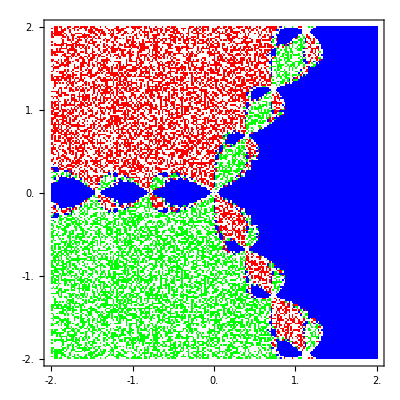

```mathematica
IterMax=20;
g[z_]:= z- (z^3-1)/(3 z^2)
g[0.0+0.0 ⅈ] = 0.0 +0.0 ⅈ;
n=100; 
{xMax,yMax}={2.0,2.0};
{xMin,yMin}=-{xMax,yMax};
{Δx,Δy}={xMax,yMax}/n;
AbsoluteTiming[
Data=ParallelTable[Nest[g,x + I y,IterMax],
{y, yMin, yMax, Δy},
{x,yMin,xMax, Δx}];]
MatrixPlot[Data,
ColorRules->{-0.5-0.8660254037844386 ⅈ->Red,-0.5+0.8660254037844386 ⅈ->Green, 1.0+0.0 ⅈ->Blue},
DataRange->{{-xMax,xMax},{-yMax,yMax}}]
```